```mathematica
ClearAll["Global`*"]
```

```mathematica
a=0.2;
b=0.1;
```

```mathematica
L=1.243457513715507;
```

```mathematica
f[t_]:={0.5+a Cos[2π t](1-Sin[2π t ]),0.5+ b Sin[2 π t](1+Cos[2 π t])}
```

```mathematica
λ[t_]:=NIntegrate[Norm[f'[s]],{s,0,t}]
```

```mathematica
u01[x_]:=x[[1]]+2*x[[2]]
```

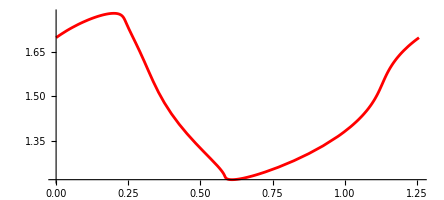

```mathematica
plotex=ParametricPlot[{λ[t],u01[f[t]]},{t,0,1},PlotStyle->Red]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_0_1_on_1.csv"]
t= Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

```mathematica
f[0]
```

{0.7,0.5}

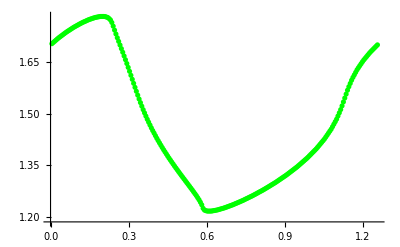

```mathematica
plotnum=ListPlot[t,PlotStyle->Green]
```

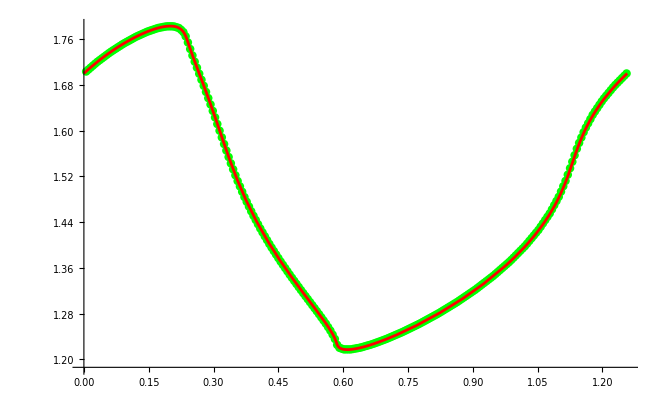

```mathematica
Show[plotnum,plotex]
```